{{-1,0,12,0,-48,0,64},{0,0,0,0,0,0,0},{-15,0,-96,0,192,0,0},{0,0,0,0,0,0,0},{-48,0,192,0,0,0,0},{0,0,0,0,0,0,0},{64,0,0,0,0,0,0}}

{{{{-1,1}},{{0,1}},{{2,2},{3,1}},{{0,1}},{{-1,1},{2,4},{3,1}},{{0,1}},{{2,6}}},{{{0,1}},{{0,1}},{{0,1}},{{0,1}},{{0,1}},{{0,1}},{{0,1}}},{{{-1,1},{3,1},{5,1}},{{0,1}},{{-1,1},{2,5},{3,1}},{{0,1}},{{2,6},{3,1}},{{0,1}},{{0,1}}},{{{0,1}},{{0,1}},{{0,1}},{{0,1}},{{0,1}},{{0,1}},{{0,1}}},{{{-1,1},{2,4},{3,1}},{{0,1}},{{2,6},{3,1}},{{0,1}},{{0,1}},{{0,1}},{{0,1}}},{{{0,1}},{{0,1}},{{0,1}},{{0,1}},{{0,1}},{{0,1}},{{0,1}}},{{{2,6}},{{0,1}},{{0,1}},{{0,1}},{{0,1}},{{0,1}},{{0,1}}}}

1

-1-15 x^2-48 x^4+64 x^6+12 y^2-96 x^2 y^2+192 x^4 y^2-48 y^4+192 x^2 y^4+64 y^6

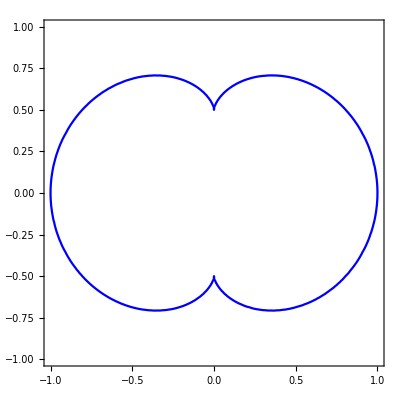

```mathematica
ClearAll["Global`*"];
a=3;
(* We substitute x by (a+1)x and y by (a+1)y *)
F[x_,y_,z_]:=-(a+1)(x+I*y)+a*z+z^a;
G[x_,y_,z_]:=-(a+1)(x-I*y)z^a+a*z^(a-1)+1;
det=Resultant[F[x,y,z],G[x,y,z],z]/(a+1)^(a-1)/(-4)^(Mod[a,2]);
cl=CoefficientList[det,{x,y}];
Print[cl];
Print[FactorInteger[cl]];
Print[GCD[Sequence@@Flatten[cl]]];
Poly[x_,y_]:=Internal`FromCoefficientList[cl,{x,y}];
Print[Poly[x,y]];
ContourPlot[0==Poly[x,y],{x,-1,1},{y,-1,1}, ContourStyle->Blue]
```